AASTriangles

FindNestedTransientRepeat

WithDatedResourceFunctions

OrderlessCombinations

SolarIrradianceData

IntegerPalindromeQ

Arity

WeightedSimpleGraph

FindHeadArities

LifetimeChart

SetAlarm

MagicSquare

MagicCube

Alphametic

IntegrateAlgebraic

Ideas

Ulam plot

ulam[n_]:=Partition[Permute[Range[n^2],Accumulate[Take[Flatten[{{n^2+1}/2,
Table[(-1)^j i,{j,n},{i,{-1,n}},{j}]}],n^2]]],n]
ArrayPlot[EulerPhi[ulam[141]],ColorFunction→Hue]

```mathematica
ResourceFunction["MagicCube"][3]
```

{{{8,15,19},{24,1,17},{10,26,6}},{{12,25,5},{7,14,21},{23,3,16}},{{22,2,18},{11,27,4},{9,13,20}}}

```mathematica
Image3D[Rescale[ResourceFunction["MagicCube"][9]]]
```

-Graphics3D-

```mathematica
draw3D[array_]:=Graphics3D[Raster3D@Rescale@array,Boxed->False];
GraphicsGrid[Partition[Table[draw3D@ResourceFunction["MagicCube"][n],{n,3,20}],4],ImageSize->Medium]
```

-Graphics-

```mathematica
unique5=ResourceFunction["LightsOutSolution"][5]
```

{{0,1,1,0,1},{0,1,1,1,0},{0,0,1,1,1},{1,1,0,1,1},{1,1,0,0,0}}

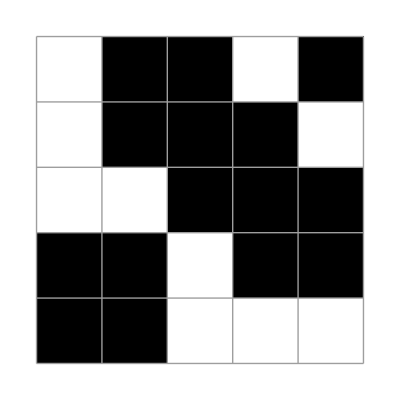

```mathematica
plot=ArrayPlot[#,Mesh->All,Frame->False]&;
plot@unique5
```

```mathematica
plot@ResourceFunction["LightsOutSolution"][35]
```

-Graphics-

```mathematica
ResourceFunction["LightsOutGame"][2]
```

```mathematica
ResourceFunction["Alphametic"]["SEND+MORE=MONEY"]
```

{{{D→7,E→5,M→1,N→6,O→0,R→8,S→9,Y→2},9567+1085=10652}}

```mathematica
{{-Graphics-, UnitSystemTransform}}[Quantity[1,(("Amperes")^4 ("Seconds")^11)/(("Kilograms")^4 ("Meters")^7)],{Quantity[1,"RydbergConstant"],Quantity[1,"SpeedOfLight"],Quantity[1,"ReducedPlanckConstant"],Quantity[1,"JosephsonConstant"],Quantity[1,"VonKlitzingConstant"]}]
```

{7.144009102×10^-6 K_J^4/(R_∞^4 c^3),2.895357833×10^-6 /(R_∞^4 ℏ^2 c^3 R_K^2),0.00001122178326 K_J^6 ℏ R_K/(R_∞^4 c^3)}

```mathematica
ResourceFunction["PivotedLUDecomposition"]
```